```mathematica
beta=0;
```

```mathematica
Erbeta
```

2.

```mathematica
gs=Range[0.01,0.25,0.025]
```

{0.01,0.035,0.06,0.085,0.11,0.135,0.16,0.185,0.21,0.235}

================= gg = 0.01=================

================= gg = 0.11=================

================= gg = 0.21=================

================= gg = 0.31=================

================= gg = 0.41=================

================= gg = 0.51=================

================= gg = 0.61=================

================= gg = 0.71=================

================= gg = 0.81=================

================= gg = 0.91=================

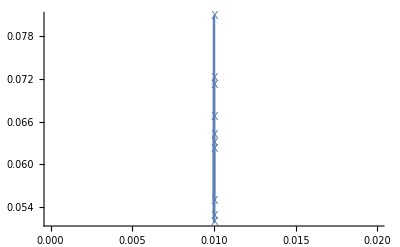

mean = {0.175,0.155,0.17,0.18,0.2,0.155,0.17,0.185,0.155,0.17}

{{0.01,0.175},{0.11,0.155},{0.21,0.17},{0.31,0.18},{0.41,0.2},{0.51,0.155},{0.61,0.17},{0.71,0.185},{0.81,0.155},{0.91,0.17}}

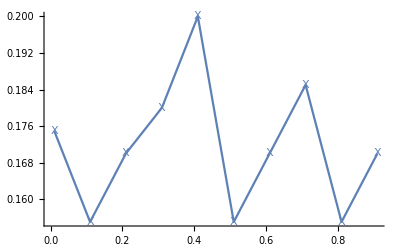

```mathematica
maxiter=200;
current={};
gs=Range[0.01,1,0.1];(*{0.05,0.1,0.5,1,2}*);
res={};allout={};
Do[
Print["================= gg = ",gg,"================="];
out=trajectory4[5,vars,gg,th,tl,Jh,Jl,kappa,gamma,maxiter];
x=out[[1]][[;;,3]];
AppendTo[res,x];
AppendTo[allout,out];

{out2,Evst}=out;
charges=out2[[All,3]];
tottime=out2[[-1,2]];
AppendTo[current,{gs[[i]],Total[charges]/tottime}];
,{gg,gs}];

ListPlot[current,Joined->True,PlotMarkers->{"X"}]


mean=Mean[res//Transpose]//N;
Print["mean = ",mean];

x=Join[{gs}//Transpose,{mean}//Transpose,2]//N
ListPlot[x,Joined->True,PlotMarkers->{"X"}]
```

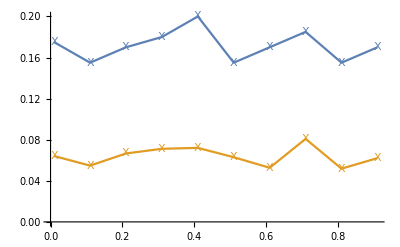

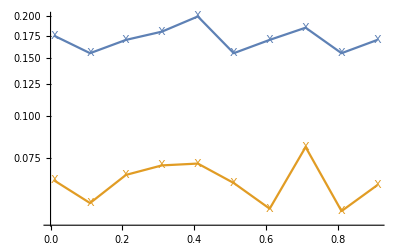

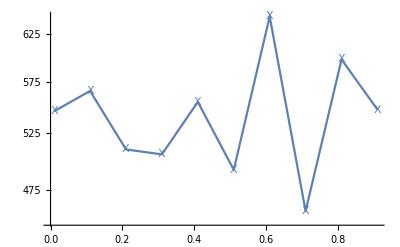

-Graphics-

-Graphics-

-Graphics-

```mathematica
current={};time={};Rate={};
gs=Range[0.01,1,0.1];(*{0.05,0.1,0.5,1,2}*);
Do[
{out2,Evst}=allout[[i]];
charges=out2[[All,3]];
tottime=out2[[-1,2]];
AppendTo[time,{gs[[i]],tottime}];
AppendTo[current,{gs[[i]],Total[charges]/tottime}];
AppendTo[Rate,out2[[All,10]]//Transpose//Total];

,{i,1,Length[allout]}];
ListPlot[{x,current},Joined->True,PlotMarkers->{"X"}]
ListLogPlot[{x,current},Joined->True,PlotMarkers->{"X"}]
ListLogPlot[time,Joined->True,PlotMarkers->{"X"}]
```

```mathematica
ListPlot[Rate,PlotMarkers->{"x"}]
```

-Graphics-

```mathematica
Dimensions[Transpose[Rate]]
```

{500,30}

```mathematica
Manipulate[ListLogPlot[Rate[[i]],PlotRange->{{1,200},{0,0.7}}],{i,1,10,1}]
```

```mathematica
Manipulate[ListLogPlot[Rate[[i]],PlotRange->{{1,500},{10^-30,10}}],{i,1,30,1}]
```

```mathematica
Manipulate[ListLogPlot[Transpose[Rate][[i]]],{i,1,500,1}]
```

-Graphics-

```mathematica
ListLogPlot[{x,current},Joined->True,PlotMarkers->{"X"}]
```

-Graphics-

-Graphics-

```mathematica
(* fractional rate of current contributiong jumps .... plot and see how it behaves with g *)
```

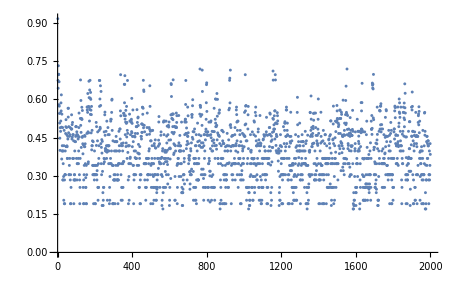

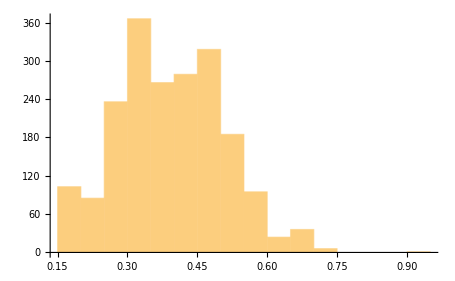

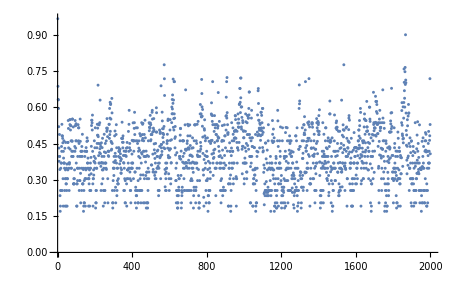

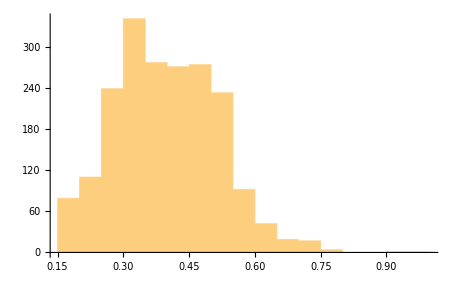

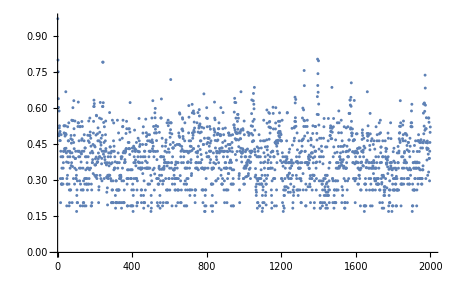

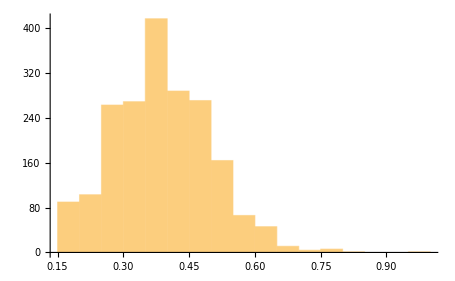

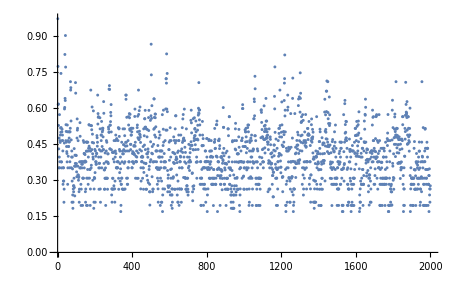

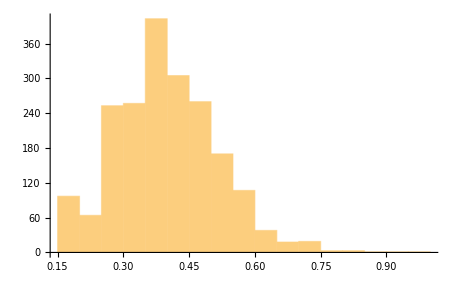

```mathematica
gs=Range[0.01,0.25,0.01];(*{0.05,0.1,0.5,1,2}*);
Do[
{out2,Evst}=allout[[i]];
x=Total[out2[[All,10]]//Transpose];
ListPlot[x]//Print;
(*Dimensions[x]//Print;*)
Histogram[x]//Print;
,{i,1,Length[allout]}]
```

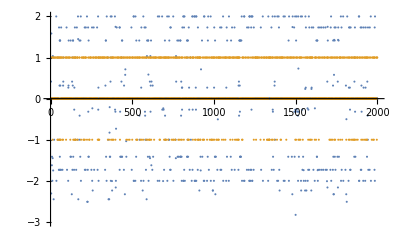

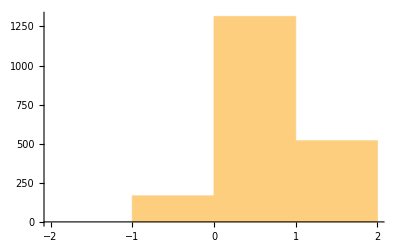

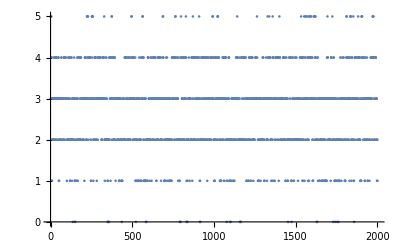

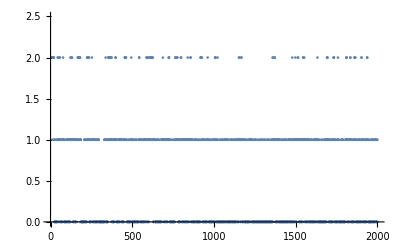

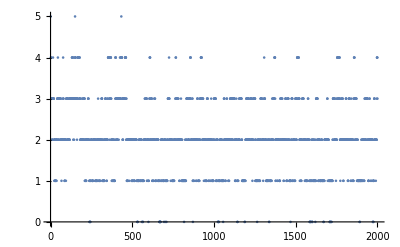

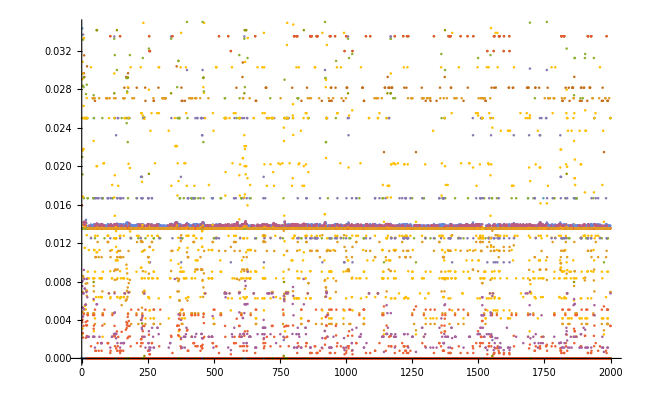

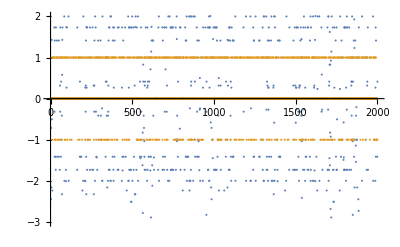

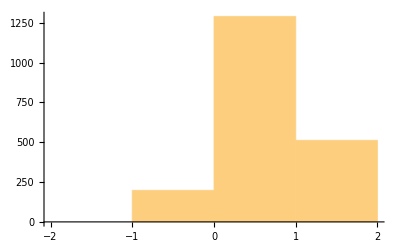

-Graphics-

-Graphics-

-Graphics-

«81 more identical outputs»

```mathematica
gs=Range[0.01,0.25,0.01];(*{0.05,0.1,0.5,1,2}*);
Do[
{out2,Evst}=allout[[i]];
current=out2[[All,3]];
(*{ITER,t,Current[[wj]],dt,Ds,Phis,NN,m,Length[Ds]+m,totrates,whichjump,whichsec}=out2*)
ListPlot[{Evst/gs[[i]],current},PlotRange->{-3,2}]//Print;
Histogram[current]//Print;
ListPlot[out2[[All,7]]]//Print;
ListPlot[out2[[All,8]]]//Print;
ListPlot[out2[[All,9]]]//Print;
ListPlot[Total[out2[[All,10]]//Transpose]]//Print;

,{i,1,Length[allout]}]
```